## Catalog, constants and grid

```mathematica
SetDirectory[NotebookDirectory[]];
$HistoryLength=0;

catalog= Import["catalogo.csv", "Table"];          (*Import the catalog and save it in a table format*)
redshift=catalog[[2;;,1]];                                             (*Redshift*)
dL= catalog[[2;;,2]];                                                          (*Luminosity distance*)
σdL= catalog[[2;;,3]];                                                        (*Sdt = standard deviation*)
nsn=Length[redshift];                                                       (*Number of supernovae in the catalog*)

c= 2.998*10^5;                                                                          (*Speed ​​of light:  Kms^-1*)
DH[H0_]= c/H0;                                                                       (*Hubble Distance: 4380 +/- 150 Mpc*)
ΩL[Ωm_,Ωκ_]:= 1- Ωm - Ωκ;              

ϵm=10^-6;
ϵk=10^-6;
ϵh=10^-6;

{Ωmdim,Ωκdim,H0dim}=3{1,1,1};                       
Ωmvec={0.3 -ϵm,0.3, 0.3+ ϵm};
Ωκvec={-ϵk, 0, ϵk};
H0vec={70- ϵh, 70, 70 + ϵh};
```

## Distance equations

```mathematica
Ez[z_,Ωm_,Ωκ_]:= √(Ωm *(1+z)^3+ Ωκ*(1+z)^2+ ΩL[Ωm,Ωκ])

Ezvec[Ωm_,Ωκ_]:=Map[Ez[#,Ωm,Ωκ]&, redshift];

DMalt[Ωm_,Ωκ_,H0_,DCvec_]:=Module[{DCsol},
Which[Ωκ<0,DH[H0]/(√Abs[(Ωκ)])*Sin[√Abs[Ωκ]*(DCvec/DH[H0])],
Ωκ==0, DCvec,
Ωκ>0,DH[H0]/(√Ωκ)*Sinh[√Ωκ*(DCvec/DH[H0])]]]
DLalt[Ωm_,Ωκ_,H0_,DCvec_]:=(1+redshift)* DMalt[Ωm,Ωκ,H0,DCvec];

derivadaDL[Ωm_,Ωκ_,H0_,DCvar_]:=Which[
Ωκ<0,DMalt[Ωm,Ωκ,H0,DCvec] + (1+redshift)* Cos[√Abs[Ωκ]*(DCvar/DH[H0])]*DH[H0]/Ezvec[Ωm,Ωκ],
Ωκ==0,DMalt[Ωm,Ωκ,H0,DCvec] + (1+redshift)* DH[H0]/Ezvec[Ωm,Ωκ] ,

Ωκ>0, DMalt[Ωm,Ωκ,H0,DCvec] + (1+redshift)* Cosh[√Ωκ*(DCvar/DH[H0])]*DH[H0]/Ezvec[Ωm,Ωκ] ];
```

## σ_z and loglikelihood

```mathematica
σz[z_]:=0.01*(1+z);                                    
σzvecnew=Map[σz[#]&, redshift];

σtotvec[Ωm_,Ωκ_,H0_,DCvec_] := √((derivadaDL[Ωm, Ωκ, H0,DCvec])^2*(σzvecnew)^2 + (σdL)^2);
zmax=0.7;

AbsoluteTiming[loglikelihoodtable= ParallelTable[
{Ωm,Ωκ,H0}={Ωmvec[[i]],Ωκvec[[j]],H0vec[[k]]};
If[(Ωm (1+zmax)^3+ Ωκ(1+zmax)^2+ ΩL[Ωm,Ωκ])<0,{Ωm,Ωκ,H0,10.^8},
DCsol=NDSolve[{Dc'[z]== 1/Ez[z,Ωm,Ωκ],Dc[0]==0}, Dc,{z,0,Max[redshift]}][[1,1,2]];
DCvec=DH[H0]Map[DCsol,redshift];
loglikelihood[Ωm_,Ωκ_,H0_,DCvec_] :=-1/2 * Total[(dL - DLalt[Ωm,Ωκ,H0,DCvec])^2/σtotvec[Ωm,Ωκ,H0,DCvec]^2];
{Ωm,Ωκ,H0,loglikelihood[Ωm,Ωκ,H0,DCvec]}],
  {i,1,Ωmdim},{j,1,Ωκdim},{k,1,H0dim}];]
```

{0.941485,Null}

```mathematica
loglikelihoodtable
```

{{{{0.299999,-1/1000000,69999999/1000000,-0.0217921},{0.299999,-1/1000000,70,-0.0217902},{0.299999,-1/1000000,70000001/1000000,-0.0217884}},{{0.299999,0,69999999/1000000,-0.0217769},{0.299999,0,70,-0.0217751},{0.299999,0,70000001/1000000,-0.0217732}},{{0.299999,1/1000000,69999999/1000000,-0.0217618},{0.299999,1/1000000,70,-0.0217599},{0.299999,1/1000000,70000001/1000000,-0.0217581}}},{{{0.3,-1/1000000,69999999/1000000,-0.0217638},{0.3,-1/1000000,70,-0.021762},{0.3,-1/1000000,70000001/1000000,-0.0217601}},{{0.3,0,69999999/1000000,-0.0217487},{0.3,0,70,-0.0217468},{0.3,0,70000001/1000000,-0.021745}},{{0.3,1/1000000,69999999/1000000,-0.0217335},{0.3,1/1000000,70,-0.0217317},{0.3,1/1000000,70000001/1000000,-0.0217298}}},{{{0.300001,-1/1000000,69999999/1000000,-0.0217356},{0.300001,-1/1000000,70,-0.0217337},{0.300001,-1/1000000,70000001/1000000,-0.0217319}},{{0.300001,0,69999999/1000000,-0.0217205},{0.300001,0,70,-0.0217186},{0.300001,0,70000001/1000000,-0.0217168}},{{0.300001,1/1000000,69999999/1000000,-0.0217053},{0.300001,1/1000000,70,-0.0217035},{0.300001,1/1000000,70000001/1000000,-0.0217016}}}}

## Fisher Matrix

### Montando a matriz

```mathematica
Lmplusϵ=loglikelihoodtable[[3,2,2,4]]  (*L(Ωm+ϵ,Ωκ,H0): incremento no Ωm e todo o resto fiducial*)  ;

Lkplusϵ= loglikelihoodtable[[2,3,2,4]]   (*L(Ωm,Ωκ+ϵ,H0): incremento no Ωκ e todo o resto fiducial*)  ;

Lhplusϵ= loglikelihoodtable[[2,2,3,4]]   (*L(Ωm,Ωκ,H0+ϵ): incremento no H0 e todo o resto fiducial*);

Lf= loglikelihoodtable[[2,2,2,4]]  (*L(ΩM, Ωκ,H0) : todo mundo fiducial*);

Lmminusϵ= loglikelihoodtable[[1,2,2,4]]  (*L(Ωm-ϵ,Ωκ,H0): decremento no Ωm e todo o resto fiducial*);

Lkminusϵ= loglikelihoodtable[[2,1,2,4]]   (*L(Ωm,Ωκ-ϵ,H0): decremento no Ωκ e todo o resto fiducial*);

Lhminusϵ= loglikelihoodtable[[2,2,1,4]]    (*L(Ωm,Ωκ,H0-ϵ): decremento no H0 e todo o resto fiducial*);
(*-------------------------------------------------------------------------------------------*)

Lmkplusϵ= loglikelihoodtable[[3,3,2,4]]    (*L(Ωm+ϵ,Ωκ+ϵ,H0): incremento no Ωm e Ωκ, H0 fiducial*);

Lmhplusϵ= loglikelihoodtable[[3,2,3,4]]    (*L(Ωm+ϵ,Ωκ,H0+ϵ): incremento no Ωm e H0, Ωκ fiducial*);

Lkhplusϵ= loglikelihoodtable[[2,3,3,4]]    (*L(Ωm,Ωκ+ϵ,H0+ϵ): incremento no Ωκ e H0, Ωm fiducial*);
(*-------------------------------------------------------------------------------------------*)

Lmkminusϵ= loglikelihoodtable[[1,1,2,4]]    (*L(Ωm-ϵ,Ωκ-ϵ,H0): decremento no Ωm e Ωκ, H0 fiducial*);

Lmhminusϵ= loglikelihoodtable[[1,2,1,4]]     (*L(Ωm-ϵ,Ωκ,H0-ϵ): decremento no Ωm e H0, Ωκ fiducial*);

Lkhminusϵ= loglikelihoodtable[[2,1,1,4]]     (*L(Ωm,Ωκ-ϵ,H0-ϵ): decremento no Ωκ e H0, Ωm fiducial*);
(*-------------------------------------------------------------------------------------------*)

Lmϵk = loglikelihoodtable[[3,1,2,4]]    (* L(Ωm+ϵ,Ωκ-ϵ,H0) : incremento em Ωm, decremento em Ωk e H0 fiducial*);

Lϵmk = loglikelihoodtable[[1,3,2,4]]     (* L(Ωm-ϵ,Ωκ+ϵ,H0) : decremento em Ωm, incremento em Ωk e H0 fiducial*);

Lmϵh= loglikelihoodtable[[3,2,1,4]]   (* L(Ωm+ϵ,Ωκ,H0-ϵ) : incremento em Ωm, decremento em H0 e Ωκ fiducial*);

Lϵmh = loglikelihoodtable[[1,2,3,4]]    (* L(Ωm-ϵ,Ωκ,H0+ϵ) : decremento em Ωm, incremento em H0 e Ωκ fiducial*);

Lkϵh= loglikelihoodtable[[2,3,1,4]]      (* L(Ωm,Ωκ+ϵ,H0-ϵ) : incremento em Ωκ, decremento em H0 e Ωm fiducial*);

Lϵkh = loglikelihoodtable[[2,1,3,4]]      (* L(Ωm,Ωκ-ϵ,H0+ϵ) : decremento em Ωκ, incremento em H0 e Ωm fiducial*);
```

```mathematica
L11= (Lmplusϵ - 2 Lf + Lmminusϵ)/ϵm^2;

L22= (Lkplusϵ - 2 Lf + Lkminusϵ)/ϵk^2;

L33= (Lhplusϵ - 2 Lf + Lhminusϵ)/ϵh^2;

L12=(Lmkplusϵ - Lmϵk - Lϵmk+ Lmkminusϵ)/(4ϵm ϵk);

L13= (Lmhplusϵ - Lmϵh - Lϵmh + Lmhminusϵ)/ (4 ϵm ϵh);

L21 = (Lmkplusϵ - Lmϵk - Lϵmk+ Lmkminusϵ)/(4ϵm ϵk) ; (*L21 = L12*)

L23 = (Lkhplusϵ - Lkϵh - Lϵkh + Lkhminusϵ)/(4 ϵk ϵh);

L31 =  (Lmhplusϵ - Lmϵh - Lϵmh + Lmhminusϵ)/ (4 ϵm ϵh);    (*L31 = L13*)

L32 = (Lkhplusϵ - Lkϵh - Lϵkh + Lkhminusϵ)/(4 ϵk ϵh);   (*L32 = L23*)
```

```mathematica
fisherMatrix = - {{L11,L12, L13},{L21,L22, L23},{L31,L32, L33}}
```

{{18344.7,9823.87,1193.92},{9823.87,5284.22,651.61},{1193.92,651.61,86.388}}

```mathematica
autovalores=Eigenvalues[fisherMatrix]    (*Verifica se a matriz de fisher está positivo-definida*)
```

{23689.1,24.5,1.67633}

```mathematica
inversefisher=Inverse[fisherMatrix];
```

```mathematica
√Diagonal[inversefisher]
```

{0.181067,0.40467,0.663972}

### Marginalizando

```mathematica
margiH0=Drop[inversefisher,{3},{3}]   (*Retirando linha e coluna referente a H0-matriz Ωm-Ωκ*);

margiΩm=Drop[inversefisher,{1},{1}]    (*Retirando linha e coluna referente a Ωm-matriz Ωκ-H0*);

margiΩκ=Drop[inversefisher,{2},{2}]    (*Retirando linha e coluna referente a Ωκ-matriz Ωm-H0*);
```

### Grid II e newlikelihood

```mathematica
Fishermk=Inverse[margiH0];
Fisherkh= Inverse[margiΩm];
Fishermh=Inverse[margiΩκ];
```

GRID II

```mathematica
{Ωmdim,Ωκdim,H0dim}=50{1,1,1};               
{Ωmmin, Ωmmax}= {0,1};
{Ωκmin,Ωκmax}={-1.2,1.2};   
{H0min, H0max}={67,73};          
ΔΩm= (Ωmmax-Ωmmin)/(Ωmdim-1);                                                   
ΔΩκ=(Ωκmax-Ωκmin)/(Ωκdim-1);
ΔH0=(H0max-H0min)/(H0dim-1);
Ωmvec=Range[Ωmmin,Ωmmax, ΔΩm];
Ωκvec=Range[Ωκmin,Ωκmax,ΔΩκ];
H0vec=Range[H0min,H0max,ΔH0];
```

```mathematica
(*...........................................................................................................................*)
```

```mathematica
Ωmf=0.3;
Ωκf= 0;
H0f= 70;
```

```mathematica
likelihoodExpressionmk[Ωm_,Ωκ_]:=Exp[-1/(2)*{Ωm-Ωmf,Ωκ-Ωκf}. Fishermk .{Ωm-Ωmf,Ωκ-Ωκf}]; 
likelihoodExpressionmh[Ωm_,H0_]:=Exp[-1/(2)*{Ωm-Ωmf,H0-H0f}. Fishermh .{Ωm-Ωmf,H0-H0f}]; 
likelihoodExpressionkh[Ωκ_,H0_]:=Exp[-1/(2)*{Ωκ-Ωκf,H0-H0f}. Fisherkh .{Ωκ-Ωκf,H0-H0f}];
```

```mathematica
newlikelihoodtablemk= Table[{Ωmvec[[i]],Ωκvec[[j]],likelihoodExpressionmk[Ωmvec[[i]],Ωκvec[[j]]]},  {i,1,Ωmdim},{j,1,Ωκdim}];
newlikelihoodtablemh= Table[{Ωmvec[[i]],H0vec[[k]],likelihoodExpressionmh[Ωmvec[[i]],H0vec[[k]]]},  {i,1,Ωmdim},{k,1,H0dim}];
newlikelihoodtablekh= Table[{Ωκvec[[j]],H0vec[[k]],likelihoodExpressionkh[Ωκvec[[j]],H0vec[[k]]]},  {j,1,Ωκdim},{k,1,H0dim}];
```

General::munfl: Exp[-727.504] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-724.989] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-761.218] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
newlikelihoodtablemk//Dimensions
newlikelihoodtablemh//Dimensions
newlikelihoodtablekh//Dimensions
MinMax[newlikelihoodtablemk[[All,All,3]]]
MinMax[newlikelihoodtablemh[[All,All,3]]]
MinMax[newlikelihoodtablekh[[All,All,3]]]
```

{50,50,3}

{50,50,3}

{50,50,3}

{0.,0.987469}

{4.1376×10^-37,0.995709}

{3.67973×10^-44,0.995088}

```mathematica
flatlikelihoodmk= Flatten[newlikelihoodtablemk,1];
flatlikelihoodmh= Flatten[newlikelihoodtablemh,1];
flatlikelihoodkh= Flatten[newlikelihoodtablekh,1];
```

```mathematica
flatlikelihoodmk//Dimensions
flatlikelihoodmh//Dimensions
flatlikelihoodkh//Dimensions
```

{2500,3}

{2500,3}

{2500,3}

```mathematica
flatlikelihoodmk[[All,3]]=-Log[flatlikelihoodmk[[All,3]]+10^-300.];  
flatlikelihoodmh[[All,3]]=-Log[flatlikelihoodmh[[All,3]]+10^-300.];  
flatlikelihoodkh[[All,3]]=-Log[flatlikelihoodkh[[All,3]]+10^-300.];
```

## ContourPlot

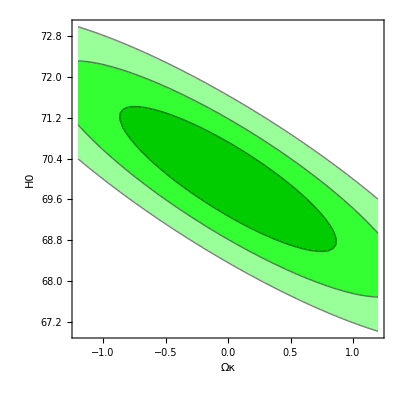

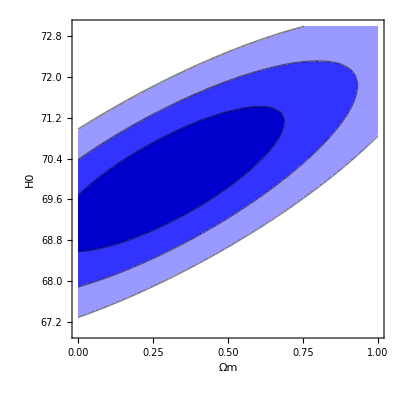

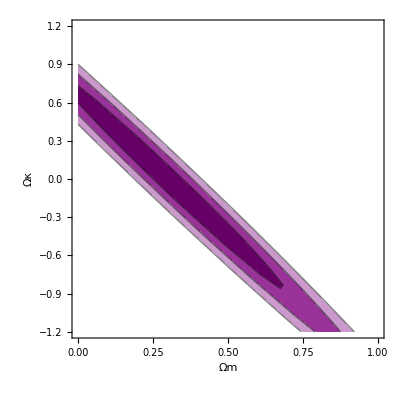

```mathematica
plot1=ListContourPlot[flatlikelihoodkh,PlotRange->All,Contours->{2.3,6.1,11.7},ContourShading->{Darker[Green,.2],Lighter[Green,.2],Lighter[Green,.6],White},Frame->True,FrameLabel->{"Ωκ","H0"}]

plot2=ListContourPlot[flatlikelihoodmh,PlotRange->All,Contours->{2.3,6.1,11.7},ContourShading->{Darker[Blue,.2],Lighter[Blue,.2],Lighter[Blue,.6],White},Frame->True,FrameLabel->{"Ωm","H0"}]

plot3=ListContourPlot[flatlikelihoodmk,PlotRange->All,Contours->{2.3,6.1,11.7},ContourShading->{Darker[Purple,.2],Lighter[Purple,.2],Lighter[Purple,.6],White},Frame->True,FrameLabel->{"Ωm","Ωκ"}]
```

```mathematica
Export["FM_I_0.01.list",flatlikelihoodkh,"List"];
Export["FM_II_0.01.list",flatlikelihoodmh,"List"];
Export["FM_III_0.01.list",flatlikelihoodmk,"List"];
```